Piecewise[{{0, x<0}, {x, x>0}, {0, True}}]

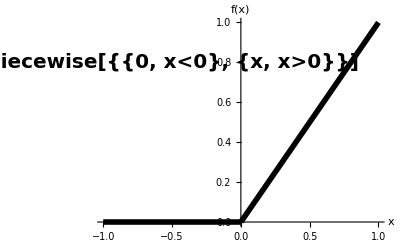

Piecewise[{{0, x<0}, {1, x>0}, {Indeterminate, True}}]

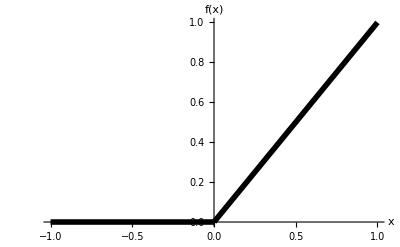

Piecewise[{{0, x<0}, {1, x>0}, {Indeterminate, True}}]

```mathematica
ReLU=Piecewise[{{0,x<0},{x,x>0}}]
Plot[ReLU,{x,-1,1},PlotStyle->{Thickness[0.01],{Black}},AxesLabel->{Style["x",Bold,Black,16],Style["f(x)",Bold,16]},Epilog->Text[Style[ReLU,Bold,20,FontFamily->"Helvetica"],{-.5,.8}]]
D[ReLU,x]
```

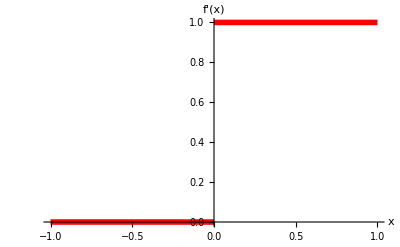

```mathematica
Plot[Out[183],{x,-1,1},PlotStyle->{Thickness[0.01],{Red}},AxesLabel->{Style["x",Bold,Black,16],Style["f'(x)",Bold,16]}]
```

Piecewise[{{x/100, x<0}, {x, x>0}, {0, True}}]

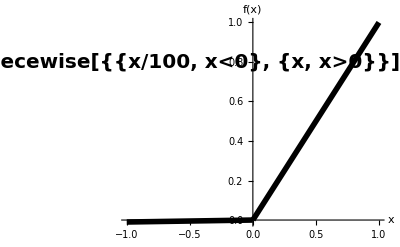

Piecewise[{{1/100, x<0}, {1, x>0}, {Indeterminate, True}}]

```mathematica
lReLU100=Piecewise[{{x/100,x<0},{x,x>0}}]
Plot[lReLU100,{x,-1,1},PlotStyle->{Thickness[0.01],{Black}},AxesLabel->{Style["x",Bold,Black,16],Style["f(x)",Bold,16]},Epilog->Text[Style[lReLU100,Bold,20,FontFamily->"Helvetica"],{-.5,.8}]]
D[lReLU100,x]
```

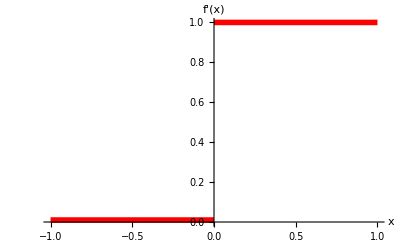

```mathematica
Plot[Out[216],{x,-1,1},PlotStyle->{Thickness[0.01],{Red}},AxesLabel->{Style["x",Bold,Black,16],Style["f'(x)",Bold,16]}]
```

Piecewise[{{0.181818 x, x<0}, {x, x>0}, {0, True}}]

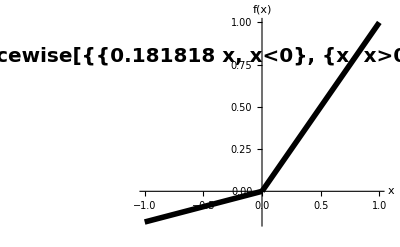

Piecewise[{{0.181818, x<0}, {1, x>0}, {Indeterminate, True}}]

```mathematica
lReLU5=Piecewise[{{x/5.5,x<0},{x,x>0}}]
Plot[lReLU5,{x,-1,1},PlotStyle->{Thickness[0.01],{Black}},AxesLabel->{Style["x",Bold,Black,16],Style["f(x)",Bold,16]},Epilog->Text[Style[lReLU5,Bold,20,FontFamily->"Helvetica"],{-.5,.8}]]
D[lReLU5,x]
```

Piecewise[{{0.181818, x<0}, {1, x>0}, {Indeterminate, True}}]

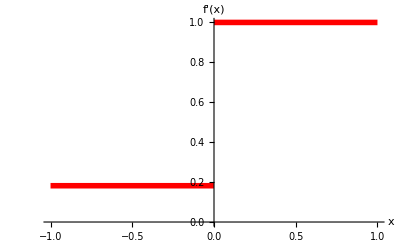

```mathematica
Piecewise[{{0.18181818181818182, x<0}, {1, x>0}, {Indeterminate, True}}]
Plot[Out[228],{x,-1,1},PlotStyle->{Thickness[0.01],{Red}},AxesLabel->{Style["x",Bold,Black,16],Style["f'(x)",Bold,16]},AxesOrigin->{0,0}]
```

```mathematica
Piecewise[{{0.18181818181818182, x<0}, {1, x>0}, {Indeterminate, True}}]
```

((-1+(1+ⅇ^x)^2) x)/(1+(1+ⅇ^x)^2)

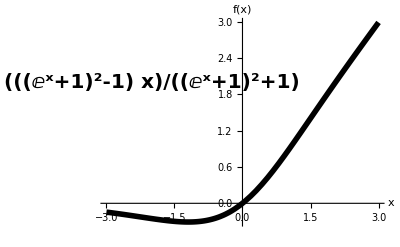

(-1+(1+ⅇ^x)^2)/(1+(1+ⅇ^x)^2)-(2 ⅇ^x (1+ⅇ^x) (-1+(1+ⅇ^x)^2) x)/((1+(1+ⅇ^x)^2)^2)+(2 ⅇ^x (1+ⅇ^x) x)/(1+(1+ⅇ^x)^2)

```mathematica
MISH=x*Tanh[Log[1+Exp[x]]]
Plot[MISH,{x,-3,3},PlotStyle->{Thickness[0.01],{Black}},AxesLabel->{Style["x",Bold,Black,16],Style["f(x)",Bold,16]},Epilog->Text[Style[MISH,Bold,20,FontFamily->"Helvetica"],{-2,2}]]
D[MISH,x]
```

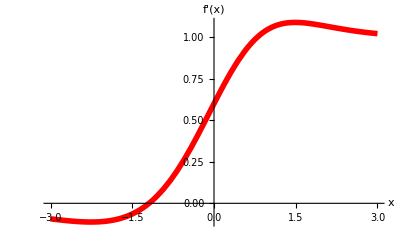

```mathematica
Plot[Out[255],{x,-3,3},PlotStyle->{Thickness[0.01],{Red}},AxesLabel->{Style["x",Bold,Black,16],Style["f'(x)",Bold,16]},AxesOrigin->{0,0}]
```

```mathematica
Plot[{Sin[x],Cos[x]},{x,0,2 π}]Graphics[Circle[]]
```

Tanh[x]

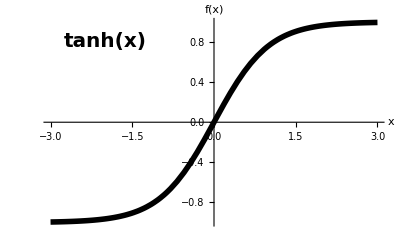

Sech[x]^2

```mathematica
TANH=Tanh[x]
Plot[TANH,{x,-3,3},PlotStyle->{Thickness[0.01],{Black}},AxesLabel->{Style["x",Bold,Black,16],Style["f(x)",Bold,16]},Epilog->Text[Style[TANH,Bold,20,FontFamily->"Helvetica"],{-2,.8}]]
D[TANH,x]
```

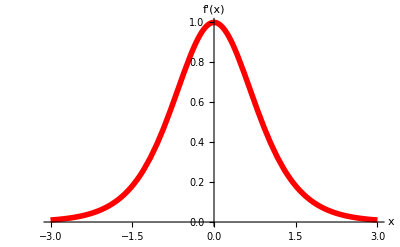

```mathematica
Plot[Out[389],{x,-3,3},PlotStyle->{Thickness[0.01],{Red}},AxesLabel->{Style["x",Bold,Black,16],Style["f'(x)",Bold,16]},AxesOrigin->{0,0}]
```

LogisticSigmoid[x]

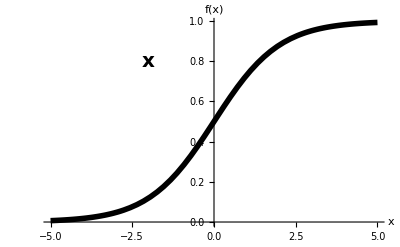

(1-LogisticSigmoid[x]) LogisticSigmoid[x]

```mathematica
SIGM=LogisticSigmoid[x]
Plot[SIGM,{x,-5,5},PlotStyle->{Thickness[0.01],{Black}},AxesLabel->{Style["x",Bold,Black,16],Style["f(x)",Bold,16]},Epilog->Text[Style[SIGM,Bold,20,FontFamily->"Helvetica"],{-2,.8}]]
D[SIGM,x]
```

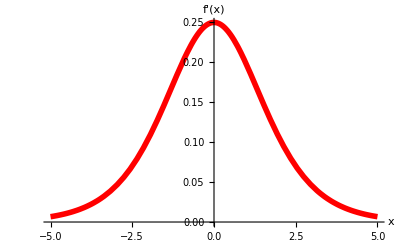

```mathematica
Plot[Out[399],{x,-5,5},PlotStyle->{Thickness[0.01],{Red}},AxesLabel->{Style["x",Bold,Black,16],Style["f'(x)",Bold,16]},AxesOrigin->{0,0}]
```